```mathematica
Clear["`*"]
SetDirectory[NotebookDirectory[]]
```

C:\Users\shiyi\work\git\work\critical_region\cheby\LPA\v2\phase\T50

```mathematica
lT=40;
startT=1;
alist=Table[Flatten[Import["./Tem"<>ToString[i]<>"/buffer/a.dat"]],{i,startT,lT}];
alist1=Table[Rest[alist[[i]]],{i,1,lT}];
```

```mathematica
ρmin=0;
ρmax=9000;
c0=1.85*10^6;
fpi=93.5;
cmax=10.^7;
cmin=10.^-2;
```

```mathematica
rhoend=400;
sigma=Table[√(2 rho),{rho,0,rhoend,rhoend/191}];
Vall=Table[Table[Evaluate[(test=SetPrecision[Sum[alist1[[i]][[n]]*Cos[n*ArcCos[(2ρ-ρmin-ρmax)/(ρmax-ρmin)]],{n,1,20}]+1/2 First[alist[[i]]],52])],{ρ,0,rhoend,rhoend/191}],{i,1,lT}];
Vdata=Table[Transpose[{sigma,Vall[[i]]-Vall[[i]][[1]]+10^7}],{i,1,lT}];
```

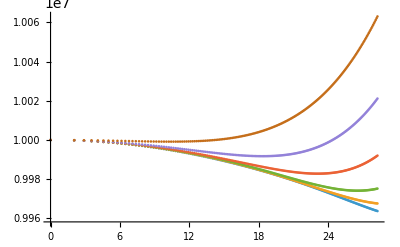

```mathematica
ListPlot[Vdata[[11;;16]],PlotRange->{All,All},ScalingFunctions->{Automatic,Automatic}]
```

```mathematica
Table[3+(i-1)0.25,{i,1,40}]
```

{3.,3.25,3.5,3.75,4.,4.25,4.5,4.75,5.,5.25,5.5,5.75,6.,6.25,6.5,6.75,7.,7.25,7.5,7.75,8.,8.25,8.5,8.75,9.,9.25,9.5,9.75,10.,10.25,10.5,10.75,11.,11.25,11.5,11.75,12.,12.25,12.5,12.75}